```mathematica
H=10^-8;
calPf=1/(2ϵfs)(H/(2π))^2
```

1/(80000000000000000 π^2 ϵfs)

```mathematica
ϵf=ϵfs/.Solve[calPf==10^-2,ϵfs][[1]]
```

1/(800000000000000 π^2)

```mathematica
ϵi=10^-2;
```

```mathematica
Nf=Log[ϵi/ϵf]/6;Nf//N
```

5.33332

```mathematica
dotphi0=dotphi0s/.Solve[ϵi==dotphi0s^2/(2 H^2),dotphi0s][[2]]
dotphif=dotphifs/.Solve[ϵf==dotphifs^2/(2 H^2),dotphifs][[2]]
```

1/(500000000 √2)

1/(2000000000000000 π)

```mathematica
phi0=-(dotphi0-dotphif)/(3H)
```

-100000000/3 (1/(500000000 √2)-1/(2000000000000000 π))

```mathematica
phiN[NN_]=phi0+dotphi0/(3H)(1-E^(-3NN));
```

```mathematica
phiN[Nf]//Simplify
```

0

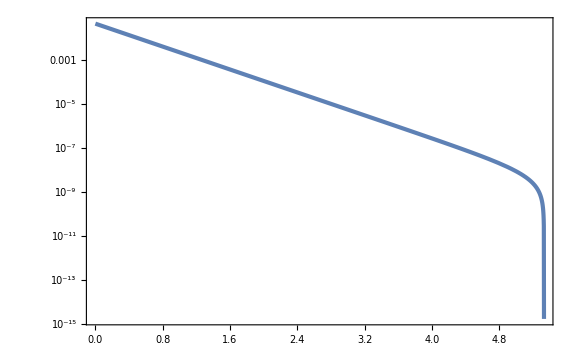

```mathematica
LogPlot[Abs[phiN[NN]],{NN,0,Nf}]
```

```mathematica
Pphi[phi_,NN_]=1/Sqrt[2π(H/(2π))^2 NN](Exp[(-(phi-phiN[NN])^2)/(2(H/(2π))^2 NN)]-Exp[(-(phi+phiN[NN])^2)/(2(H/(2π))^2 NN)]);
```

```mathematica
Pphi[phiN[1],1]//N
```

General::munfl: Exp[-4.34919×10^12] is too small to represent as a normalized machine number; precision may be lost.

2.50663×10^8

General::munfl: Exp[-5.39018×10^9] is too small to represent as a normalized machine number; precision may be lost.

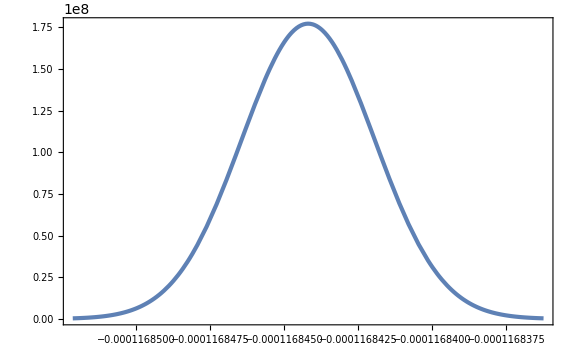

```mathematica
Plot[Pphi[phi,2],{phi,phiN[2]-5 H/(2π),phiN[2]+5 H/(2π)}]
```